```mathematica
ClearAll["Global`*"]
```

```mathematica
(*This is the code to perform calculations for LESCO. The calculations can be found in "One Note/Effect of stress on transition temperature/ Calc"*)
```

```mathematica
(*Extracting the Stress vs Strain data for LESCO*)
(*-Graphics- The units are in K and Kbar=10^8 Pa*)
```

```mathematica
P110={{-0.0846182853784988,9.89492119089317},{-0.5595319342875719,11.120840630472856},{-0.9816424405490377,12.276707530647986},{-1.540952279599396,13.782837127845884},{-2.089749610754962,15.183887915936953},{-2.5224466566569577,16.30472854640981},{-2.9234581153831027,17.390542907180386}};
P100={{-0.05341390454994477,8.949211908931698},{-0.4548510458140832,9.229422066549912},{-0.7822934572131212,9.544658493870402},{-1.1625760271326349,9.859894921190893},{-1.9759443096192686,10.560420315236426},{-2.979444623097442,11.436077057793344}};
P001={{-0.011308349161474829,8.633975481611207},{-0.2544471101014002,8.493870402802102},{-0.48701783933723075,8.353765323992993},{-0.8993006313519817,8.108581436077058},{-1.4384738355616116,7.723292469352012},{-1.988196563538903,7.373029772329247},{-2.728217893935643,6.882661996497372},{-2.9713751628120035,6.70753064798599},{-3.425967097516003,6.392294220665498},{-3.7325510645533684,6.182136602451838}};
P110[[1,2]]
Sclng:=10^8(*to convert Kbar to Pascal*)
P110[[;;,1]]=Sclng*P110[[;;,1]];
P110
P100[[;;,1]]=Sclng*P100[[;;,1]];
P100
P001[[;;,1]]=Sclng*P001[[;;,1]];
P001
```

9.89492

{{-8.46183×10^6,9.89492},{-5.59532×10^7,11.1208},{-9.81642×10^7,12.2767},{-1.54095×10^8,13.7828},{-2.08975×10^8,15.1839},{-2.52245×10^8,16.3047},{-2.92346×10^8,17.3905}}

{{-5.34139×10^6,8.94921},{-4.54851×10^7,9.22942},{-7.82293×10^7,9.54466},{-1.16258×10^8,9.85989},{-1.97594×10^8,10.5604},{-2.97944×10^8,11.4361}}

{{-1.13083×10^6,8.63398},{-2.54447×10^7,8.49387},{-4.87018×10^7,8.35377},{-8.99301×10^7,8.10858},{-1.43847×10^8,7.72329},{-1.9882×10^8,7.37303},{-2.72822×10^8,6.88266},{-2.97138×10^8,6.70753},{-3.42597×10^8,6.39229},{-3.73255×10^8,6.18214}}

```mathematica
(*Collecting Data for the lattice parameters*)
(*-Graphics-*)
a0VsT:={{139.77619532044764,5.3445833333333335},{129.8067141403866,5.3445833333333335},{119.83723296032555,5.3445833333333335},{109.8677517802645,5.344513888888889},{99.89827060020345,5.344305555555556},{89.72533062054934,5.344166666666666},{79.7558494404883,5.344236111111111},{69.78636826042727,5.344027777777778},{59.81688708036623,5.3438888888888885},{49.64394710071211,5.3438888888888885},{39.87792472024415,5.343819444444445},{29.70498474059002,5.343819444444445},{19.73550356052899,5.343819444444445},{9.766022380467952,5.3438888888888885}}
aVsT:={{149.74567650050864,5.323472222222223},{159.7151576805697,5.323819444444444},{169.88809766022382,5.324305555555555},{179.85757884028487,5.324722222222222},{190.03051881993895,5.325347222222223},{200,5.325972222222222}}
bVsT:={{149.94913530010172,5.362777777777778},{159.7151576805697,5.362847222222222},{169.88809766022382,5.362777777777778},{179.85757884028487,5.362638888888889},{190.03051881993895,5.3625},{199.79654120040692,5.362361111111111}}
c0VsT:={{139.97965412004078,13.12918216976042},{130.0101729399796,13.125449400949748},{120.04069175991862,13.123659951977132},{109.86775178026454,13.122032281580388},{100.10172939979657,13.120566883991415},{89.92878942014244,13.11893921359467},{79.95930824008138,13.117797537901408},{69.98982706002033,13.116493918888306},{60.020345879959336,13.115514186514881},{50.050864699898284,13.114858340781133},{40.081383519837175,13.114202495047383},{30.11190233977618,13.11387053595331},{19.93896236012216,13.113700355435109},{9.969481180061052,13.113692282980711}}
cVsT:={{150.1525940996949,13.126923200481052},{160.12207527975585,13.128874592773505},{170.0915564598169,13.13066404174612},{180.06103763987795,13.132615434038573},{190.03051881993906,13.134728769650865},{200,13.136842105263156}}
```

```mathematica
(*Setting up the Canonical basis vectors*)
e1:={1,0,0}
e2:={0,1,0}
e3:={0,0,1}
(*Setting up the lattice vectors for the Tetragonal and Orthorhombic Lattices and dual Cubic lattice *)
Subscript[a, 0]=a0VsT[[1,2]];
Subscript[c, 0]=c0VsT[[1,2]];
a=aVsT[[1,2]];
b=bVsT[[1,2]];
c=cVsT[[1,2]];
â=(Subscript[a, 0]^2*Subscript[c, 0])^(1/3);
Print["a_0=",Subscript[a, 0]]
Print["c_0=",Subscript[c, 0]]
Print["a=",a]
Print["b=",b]
Print["c=",c]
Print["â=",â]
rh1:=1/(â)(e1+e2)
rh2:=1/(â)(e1-e2)
rh3:=1/(â)e3
f1:=Subscript[a, 0]/2*e1+Subscript[a, 0]/2*e2
f2:=Subscript[a, 0]/2*e1-Subscript[a, 0]/2*e2
f3:=Subscript[c, 0]*e3
u1:=b/2*e1+a/2*e2
u2:=b/2*e1-a/2*e2
u3:=c*e3
(*Plotting the dual vectors for the Cubic unit cell*)
Nn=5;
N1=Nn;N2=Nn;N3=Nn;
X={};(*Size of the array storing the positions*)
For[ii=1,ii<=N1,ii++,For[jj=1,jj<=N2,jj++,For[kk=1,kk<=N3,kk++,AppendTo[X,(ii-1)/(N1-1)*rh1+(jj-1)/(N2-1)*rh2+(kk-1)/(N3-1)*rh3]]]]
Print["Checking that the dual lattice of cubic"]
Graphics3D[Sphere[X,0.005],BoxRatios->{1, 1, 1}]
Clear[X,Nn]
(*Plotting the basis vectors for the Tetragonal unit cell*)
Nn=5;
N1=Nn;N2=Nn;N3=Nn;
X={};(*Size of the array storing the positions*)
For[ii=1,ii<=N1,ii++,For[jj=1,jj<=N2,jj++,For[kk=1,kk<=N3,kk++,AppendTo[X,(ii-1)/(N1-1)*f1+(jj-1)/(N2-1)*f2+(kk-1)/(N3-1)*f3]]]]
Print["Checking that the crystal structure of Tetragonal"]
Graphics3D[Sphere[X,0.2],BoxRatios->{1, 1, Subscript[c, 0]/Subscript[a, 0]}]
Clear[X,Nn]
(*Plotting the basis vectors for the reference unit cell*)
Nn=5;
N1=Nn;N2=Nn;N3=Nn;
X={};(*Size of the array storing the positions*)
For[ii=1,ii<=N1,ii++,For[jj=1,jj<=N2,jj++,For[kk=1,kk<=N3,kk++,AppendTo[X,(ii-1)/(N1-1)*u1+(jj-1)/(N2-1)*u2+(kk-1)/(N3-1)*u3]]]]
Print["Checking that the crystal structure of Orthorhombic"]
Print["To see the orthorhombic structure, notice the bounding cell, its sizes are of different length"]
Graphics3D[Sphere[X,0.2],BoxRatios->{1, b/a, c/a}]
Clear[X,Nn]
FI:=Outer[Times,u1,rh1]+Outer[Times,u2,rh2]+Outer[Times,u3,rh3](*Outer[Times,u2,rh2]*)
Print["To check the def grad computed using Mathematica matched what we expect FI-diag(b/a_0,a/a_0,c/c_0)--->",FI-{{b/(â),0,0},{0,a/(â),0},{0,0,c/(â)}}//MatrixForm]
Print["Checking that {FI h_i=u_i(}_1)^3-->",(â)^2/2*FI.rh1-u1,(â)^2/2*FI.rh2-u2,(â)^2*FI.rh3-u3](*(â)^2/2*rh1=h1, (â)^2/2*rh2=h2, (â)^2*rh3=h3,*)
```

a_0=5.34458

c_0=13.1292

a=5.32347

b=5.36278

c=13.1269

â=7.21144

Checking that the dual lattice of cubic

-Graphics3D-

Checking that the crystal structure of Tetragonal

-Graphics3D-

Checking that the crystal structure of Orthorhombic

To see the orthorhombic structure, notice the bounding cell, its sizes are of different length

-Graphics3D-

To check the def grad computed using Mathematica matched what we expect FI-diag(b/a_0,a/a_0,c/c_0)--->(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

Checking that {FI h_i=u_i(}_1)^3-->{0.,0.,0.}{0.,0.,0.}{0.,0.,1.77636×10^-15}

```mathematica
(*Using the characterization of the Rotation matrix to determine the Symmetries if the cubic, Tetragonal and Orthorhombic phase.*)
Qq[ux_,uy_,uz_,t_]:={{Cos[t]+ux^2*(1-Cos[t]) , ux*uy*(1-Cos[t])-uz*Sin[t] , ux*uz*(1-Cos[t])+uy*Sin[t]},{ ux*uy*(1-Cos[t])+uz*Sin[t] ,Cos[t]+uy^2*(1-Cos[t]) , uy*uz*(1-Cos[t])-ux*Sin[t]},{ ux*uz*(1-Cos[t])-uy*Sin[t] , uy*uz*(1-Cos[t])+ux*Sin[t] ,Cos[t]+uz^2*(1-Cos[t])}}
```

```mathematica
Qq[-1/Sqrt[3],1/Sqrt[3],-1/Sqrt[3],4/3*Pi]//MatrixForm
```

(0 | -1 | 0
0 | 0 | -1
1 | 0 | 0)

```mathematica
(*Determining the Tetragonal and Orthorhombic wells*)
U:=DiagonalMatrix[{β,α,γ}](*In the notes this corresponds to either α=Subscript[a, 0]/(â) and β=Subscript[c, 0]/(â) or α=a/(â), β=b/(â), γ=c/(â)*)
uu1=-1/Sqrt[3];uu2=1/Sqrt[3];uu3=-1/Sqrt[3];t=4/3*Pi;
U//MatrixForm
Transpose[Qq[uu1,uu2,uu3,t]].U.Qq[uu1,uu2,uu3,t]//MatrixForm
Clear[U,uu1,uu2,uu3,t]
```

(β | 0 | 0
0 | α | 0
0 | 0 | γ)

(γ | 0 | 0
0 | β | 0
0 | 0 | α)

```mathematica
(*Checking For Twins*)
(*Defining the Deformations*)
UO1=Outer[Times,u1,rh1]+Outer[Times,u2,rh2]+Outer[Times,u3,rh3];
UO2=Transpose[Qq[0,0,1,Pi/2]].UO1.Qq[0,0,1,Pi/2];
UO3=Transpose[Qq[1,0,0,Pi/2]].UO1.Qq[1,0,0,Pi/2];
UO4=Transpose[Qq[1/Sqrt[3],1/Sqrt[3],1/Sqrt[3],(2*Pi)/3]].UO1.Qq[1/Sqrt[3],1/Sqrt[3],1/Sqrt[3],(2*Pi)/3];
UO5=Transpose[Qq[1/Sqrt[3],1/Sqrt[3],1/Sqrt[3],(4*Pi)/3]].UO1.Qq[1/Sqrt[3],1/Sqrt[3],1/Sqrt[3],(4*Pi)/3];
UO6=Transpose[Qq[0,1,0,Pi/2]].UO1.Qq[0,1,0,Pi/2];
UT1=Outer[Times,f1,rh1]+Outer[Times,f2,rh2]+Outer[Times,f3,rh3];
UT2=Transpose[Qq[1,0,0,Pi/2]].UT1.Qq[1,0,0,Pi/2];
UT3=Transpose[Qq[0,1,0,Pi/2]].UT1.Qq[0,1,0,Pi/2];
Print["UT1=",UT1//MatrixForm]
Print["UT2=",UT2//MatrixForm]
Print["UT3=",UT2//MatrixForm]
Print["UO1=",UO1//MatrixForm]
Print["UO2=",UO2//MatrixForm]
Print["UO3=",UO3//MatrixForm]
Print["UO4=",UO4//MatrixForm]
Print["UO5=",UO5//MatrixForm]
Print["UO6=",UO6//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UT2^-1UT1^2UT2^-1=",Inverse[UT2].UT1.UT1.Inverse[UT2]//MatrixForm]
Print["UT3^-1UT1^2UT3^-1=",Inverse[UT3].UT1.UT1.Inverse[UT3]//MatrixForm]
Print["UT3^-1UT2^2UT3^-1=",Inverse[UT3].UT2.UT2.Inverse[UT3]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO2^-1UO1^2UO2^-1=",Inverse[UO2].UO1.UO1.Inverse[UO2]//MatrixForm]
Print["UO3^-1UO1^2UO3^-1=",Inverse[UO3].UO1.UO1.Inverse[UO3]//MatrixForm]
Print["UO4^-1UO1^2UO4^-1=",Inverse[UO4].UO1.UO1.Inverse[UO4]//MatrixForm]
Print["UO5^-1UO1^2UO5^-1=",Inverse[UO5].UO1.UO1.Inverse[UO5]//MatrixForm]
Print["UO6^-1UO1^2UO6^-1=",Inverse[UO6].UO1.UO1.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO3^-1UO2^2UO3^-1=",Inverse[UO3].UO2.UO2.Inverse[UO3]//MatrixForm]
Print["UO4^-1UO2^2UO4^-1=",Inverse[UO4].UO2.UO2.Inverse[UO4]//MatrixForm]
Print["UO5^-1UO2^2UO5^-1=",Inverse[UO5].UO2.UO2.Inverse[UO5]//MatrixForm]
Print["UO6^-1UO2^2UO6^-1=",Inverse[UO6].UO2.UO2.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO4^-1UO3^2UO4^-1=",Inverse[UO4].UO3.UO3.Inverse[UO4]//MatrixForm]
Print["UO5^-1UO3^2UO5^-1=",Inverse[UO5].UO3.UO3.Inverse[UO5]//MatrixForm]
Print["UO6^-1UO3^2UO6^-1=",Inverse[UO6].UO3.UO3.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO5^-1UO4^2UO5^-1=",Inverse[UO5].UO4.UO4.Inverse[UO5]//MatrixForm]
Print["UO6^-1UO4^2UO6^-1=",Inverse[UO6].UO4.UO4.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO6^-1UO5^2UO6^-1=",Inverse[UO6].UO5.UO5.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO1^-1UT1^2UO1^-1=",Inverse[UO1].UT1.UT1.Inverse[UO1]//MatrixForm]
Print["UO2^-1UT1^2UO2^-1=",Inverse[UO2].UT1.UT1.Inverse[UO2]//MatrixForm]
Print["UO3^-1UT1^2UO3^-1=",Inverse[UO3].UT1.UT1.Inverse[UO3]//MatrixForm]
Print["UO4^-1UT1^2UO4^-1=",Inverse[UO4].UT1.UT1.Inverse[UO4]//MatrixForm]
Print["UO5^-1UT1^2UO5^-1=",Inverse[UO5].UT1.UT1.Inverse[UO5]//MatrixForm]
Print["UO6^-1UT1^2UO6^-1=",Inverse[UO6].UT1.UT1.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO1^-1UT2^2UO1^-1=",Inverse[UO1].UT2.UT2.Inverse[UO1]//MatrixForm]
Print["UO2^-1UT2^2UO2^-1=",Inverse[UO2].UT2.UT2.Inverse[UO2]//MatrixForm]
Print["UO3^-1UT2^2UO3^-1=",Inverse[UO3].UT2.UT2.Inverse[UO3]//MatrixForm]
Print["UO4^-1UT2^2UO4^-1=",Inverse[UO4].UT2.UT2.Inverse[UO4]//MatrixForm]
Print["UO5^-1UT2^2UO5^-1=",Inverse[UO5].UT2.UT2.Inverse[UO5]//MatrixForm]
Print["UO6^-1UT2^2UO6^-1=",Inverse[UO6].UT2.UT2.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
Print["UO1^-1UT3^2UO1^-1=",Inverse[UO1].UT3.UT3.Inverse[UO1]//MatrixForm]
Print["UO2^-1UT3^2UO2^-1=",Inverse[UO2].UT3.UT3.Inverse[UO2]//MatrixForm]
Print["UO3^-1UT3^2UO3^-1=",Inverse[UO3].UT3.UT3.Inverse[UO3]//MatrixForm]
Print["UO4^-1UT3^2UO4^-1=",Inverse[UO4].UT3.UT3.Inverse[UO4]//MatrixForm]
Print["UO5^-1UT3^2UO5^-1=",Inverse[UO5].UT3.UT3.Inverse[UO5]//MatrixForm]
Print["UO6^-1UT3^2UO6^-1=",Inverse[UO6].UT3.UT3.Inverse[UO6]//MatrixForm]
Print["-------------------------------------------------------------"]
```

UT1=(0.741126 | 0. | 0.
0. | 0.741126 | 0.
0. | 0. | 1.82061)

UT2=(0.741126 | 0. | 0.
0. | 1.82061 | 0.
0. | 0. | 0.741126)

UT3=(0.741126 | 0. | 0.
0. | 1.82061 | 0.
0. | 0. | 0.741126)

UO1=(0.743649 | 0. | 0.
0. | 0.738199 | 0.
0. | 0. | 1.82029)

UO2=(0.738199 | 0. | 0.
0. | 0.743649 | 0.
0. | 0. | 1.82029)

UO3=(0.743649 | 0. | 0.
0. | 1.82029 | 0.
0. | 0. | 0.738199)

UO4=(0.738199 | 0. | 0.
0. | 1.82029 | 0.
0. | 0. | 0.743649)

UO5=(1.82029 | 0. | 0.
0. | 0.743649 | 0.
0. | 0. | 0.738199)

UO6=(1.82029 | 0. | 0.
0. | 0.738199 | 0.
0. | 0. | 0.743649)

-------------------------------------------------------------

UT2^-1UT1^2UT2^-1=(1. | 0. | 0.
0. | 0.165711 | 0.
0. | 0. | 6.03459)

UT3^-1UT1^2UT3^-1=(0.165711 | 0. | 0.
0. | 1. | 0.
0. | 0. | 6.03459)

UT3^-1UT2^2UT3^-1=(0.165711 | 0. | 0.
0. | 6.03459 | 0.
0. | 0. | 1.)

-------------------------------------------------------------

UO2^-1UO1^2UO2^-1=(1.01482 | 0. | 0.
0. | 0.985395 | 0.
0. | 0. | 1.)

UO3^-1UO1^2UO3^-1=(1. | 0. | 0.
0. | 0.164461 | 0.
0. | 0. | 6.08045)

UO4^-1UO1^2UO4^-1=(1.01482 | 0. | 0.
0. | 0.164461 | 0.
0. | 0. | 5.99165)

UO5^-1UO1^2UO5^-1=(0.166899 | 0. | 0.
0. | 0.985395 | 0.
0. | 0. | 6.08045)

UO6^-1UO1^2UO6^-1=(0.166899 | 0. | 0.
0. | 1. | 0.
0. | 0. | 5.99165)

-------------------------------------------------------------

UO3^-1UO2^2UO3^-1=(0.985395 | 0. | 0.
0. | 0.166899 | 0.
0. | 0. | 6.08045)

UO4^-1UO2^2UO4^-1=(1. | 0. | 0.
0. | 0.166899 | 0.
0. | 0. | 5.99165)

UO5^-1UO2^2UO5^-1=(0.164461 | 0. | 0.
0. | 1. | 0.
0. | 0. | 6.08045)

UO6^-1UO2^2UO6^-1=(0.164461 | 0. | 0.
0. | 1.01482 | 0.
0. | 0. | 5.99165)

-------------------------------------------------------------

UO4^-1UO3^2UO4^-1=(1.01482 | 0. | 0.
0. | 1. | 0.
0. | 0. | 0.985395)

UO5^-1UO3^2UO5^-1=(0.166899 | 0. | 0.
0. | 5.99165 | 0.
0. | 0. | 1.)

UO6^-1UO3^2UO6^-1=(0.166899 | 0. | 0.
0. | 6.08045 | 0.
0. | 0. | 0.985395)

-------------------------------------------------------------

UO5^-1UO4^2UO5^-1=(0.164461 | 0. | 0.
0. | 5.99165 | 0.
0. | 0. | 1.01482)

UO6^-1UO4^2UO6^-1=(0.164461 | 0. | 0.
0. | 6.08045 | 0.
0. | 0. | 1.)

-------------------------------------------------------------

UO6^-1UO5^2UO6^-1=(1. | 0. | 0.
0. | 1.01482 | 0.
0. | 0. | 0.985395)

-------------------------------------------------------------

UO1^-1UT1^2UO1^-1=(0.993226 | 0. | 0.
0. | 1.00795 | 0.
0. | 0. | 1.00034)

UO2^-1UT1^2UO2^-1=(1.00795 | 0. | 0.
0. | 0.993226 | 0.
0. | 0. | 1.00034)

UO3^-1UT1^2UO3^-1=(0.993226 | 0. | 0.
0. | 0.165768 | 0.
0. | 0. | 6.08255)

UO4^-1UT1^2UO4^-1=(1.00795 | 0. | 0.
0. | 0.165768 | 0.
0. | 0. | 5.99371)

UO5^-1UT1^2UO5^-1=(0.165768 | 0. | 0.
0. | 0.993226 | 0.
0. | 0. | 6.08255)

UO6^-1UT1^2UO6^-1=(0.165768 | 0. | 0.
0. | 1.00795 | 0.
0. | 0. | 5.99371)

-------------------------------------------------------------

UO1^-1UT2^2UO1^-1=(0.993226 | 0. | 0.
0. | 6.08255 | 0.
0. | 0. | 0.165768)

UO2^-1UT2^2UO2^-1=(1.00795 | 0. | 0.
0. | 5.99371 | 0.
0. | 0. | 0.165768)

UO3^-1UT2^2UO3^-1=(0.993226 | 0. | 0.
0. | 1.00034 | 0.
0. | 0. | 1.00795)

UO4^-1UT2^2UO4^-1=(1.00795 | 0. | 0.
0. | 1.00034 | 0.
0. | 0. | 0.993226)

UO5^-1UT2^2UO5^-1=(0.165768 | 0. | 0.
0. | 5.99371 | 0.
0. | 0. | 1.00795)

UO6^-1UT2^2UO6^-1=(0.165768 | 0. | 0.
0. | 6.08255 | 0.
0. | 0. | 0.993226)

-------------------------------------------------------------

UO1^-1UT3^2UO1^-1=(5.99371 | 0. | 0.
0. | 1.00795 | 0.
0. | 0. | 0.165768)

UO2^-1UT3^2UO2^-1=(6.08255 | 0. | 0.
0. | 0.993226 | 0.
0. | 0. | 0.165768)

UO3^-1UT3^2UO3^-1=(5.99371 | 0. | 0.
0. | 0.165768 | 0.
0. | 0. | 1.00795)

UO4^-1UT3^2UO4^-1=(6.08255 | 0. | 0.
0. | 0.165768 | 0.
0. | 0. | 0.993226)

UO5^-1UT3^2UO5^-1=(1.00034 | 0. | 0.
0. | 0.993226 | 0.
0. | 0. | 1.00795)

UO6^-1UT3^2UO6^-1=(1.00034 | 0. | 0.
0. | 1.00795 | 0.
0. | 0. | 0.993226)

-------------------------------------------------------------

```mathematica
(*Energy Minimization-Loading along e1*)
(*Loading along e1 *)
Clear[e]
e=e1
Print["Compressive loading along [100] determining the SuperConducting State (Tetragonal)."]
Print["The inner minimization is achieved at ",Min[(UT1.e).(UT1.e),(UT2.e).(UT2.e),(UT3.e).(UT3.e)]]
(UT1.e)
(UT2.e)
(UT3.e)
Print["The values of (UTi(e1)^2 are, --->",{(UT1.e).(UT1.e),(UT2.e).(UT2.e),(UT3.e).(UT3.e)}]
Print["The solution was F=QU_T1,QU_T2 with Q having axis e1."]
Print["-------------------------------------------------------------"]
Print["Compressive loading along [100] determining the Normal State (Orthorhombic)."]
Print["The inner minimization is achieved at ",Min[(UO1.e).(UO1.e),(UO2.e).(UO2.e),(UO3.e).(UO3.e),(UO4.e).(UO4.e),(UO5.e).(UO5.e),(UO6.e).(UO6.e)]]
(UO1.e)
(UO2.e)
(UO3.e)
(UO4.e)
(UO5.e)
(UO6.e)
Print["The values of (UOie_1)^2 are, --->",{(UO1.e).(UO1.e),(UO2.e).(UO2.e),(UO3.e).(UO3.e),(UO4.e).(UO4.e),(UO5.e).(UO5.e),(UO6.e).(UO6.e)}]
Print["The solution was F=QU_T1,QU_T2 with Q having axis e1."]
Print["-------------------------------------------------------------"]
```

{1,0,0}

Compressive loading along [100] determining the SuperConducting State (Tetragonal).

The inner minimization is achieved at 0.549268

{0.741126,0.,0.}

{0.741126,0.,0.}

{1.82061,0.,0.}

The values of (UTi(e1)^2 are, --->{0.549268,0.549268,3.3146}

The solution was F=QU_T1,QU_T2 with Q having axis e1.

-------------------------------------------------------------

Compressive loading along [100] determining the Normal State (Orthorhombic).

The inner minimization is achieved at 0.544937

{0.743649,0.,0.}

{0.738199,0.,0.}

{0.743649,0.,0.}

{0.738199,0.,0.}

{1.82029,0.,0.}

{1.82029,0.,0.}

The values of (UOie_1)^2 are, --->{0.553014,0.544937,0.553014,0.544937,3.31346,3.31346}

The solution was F=QU_T1,QU_T2 with Q having axis e1.

-------------------------------------------------------------

```mathematica
(*Energy Minimization-Loading along (e1+e2)/(√2)*)
Clear[e]
e=(e1+e2)/Sqrt[2]
Print["Compressive loading along [110] determining the SuperConducting State (Tetragonal)."]
Print["The inner minimization is achieved at ",Min[(UT1.e).(UT1.e),(UT2.e).(UT2.e),(UT3.e).(UT3.e)]]
(UT1.e)
(UT2.e)
(UT3.e)
Print["The values of (UTi(e1+e2)/(√2))^2 are, --->",{(UT1.e).(UT1.e),(UT2.e).(UT2.e),(UT3.e).(UT3.e)}]
Print["A.UT1=",{{1,1,0},{1,1,0},{0,0,0}}.UT1]
Print["The solution was F=QU_T1 with Q having axis (e1+e2)/(√2)."]
Print["-------------------------------------------------------------"]
Print["Compressive loading along [110] determining the Normal State (Orthorhombic)."]
Print["The inner minimization is achieved at ",Min[(UO1.e).(UO1.e),(UO2.e).(UO2.e),(UO3.e).(UO3.e),(UO4.e).(UO4.e),(UO5.e).(UO5.e),(UO6.e).(UO6.e)]]
(UO1.e)
(UO2.e)
(UO3.e)
(UO4.e)
(UO5.e)
(UO6.e)
Print["The values of (UOi(e1+e2)/(√2))^2 are, --->",{(UO1.e).(UO1.e),(UO2.e).(UO2.e),(UO3.e).(UO3.e),(UO4.e).(UO4.e),(UO5.e).(UO5.e),(UO6.e).(UO6.e)}]
Print["A.UO1=",{{1,1,0},{1,1,0},{0,0,0}}.UO1]
Print["A.UO2=",{{1,1,0},{1,1,0},{0,0,0}}.UO2]
Print["In Order to get an analytical Expression, we the values as α=a/(â), β=b/(â), γ=c/(â)"]
G1={{1,1,0},{1,1,0},{0,0,0}}.DiagonalMatrix[{β,α,γ}];
G2={{1,1,0},{1,1,0},{0,0,0}}.DiagonalMatrix[{α,β,γ}];
Print["G_1=A.UO1= ",G1//MatrixForm]
Print["G_2=A.UO2= ",G2//MatrixForm]
Print["The solution still needs to be determined, cause there is slight rotation involved."]
Print["-------------------------------------------------------------"]
```

{1/(√2),1/(√2),0}

Compressive loading along [110] determining the SuperConducting State (Tetragonal).

The inner minimization is achieved at 0.549268

{0.524055,0.524055,0.}

{0.524055,1.28736,0.}

{1.28736,0.524055,0.}

The values of (UTi(e1+e2)/(√2))^2 are, --->{0.549268,1.93194,1.93194}

A.UT1={{0.741126,0.741126,0.},{0.741126,0.741126,0.},{0.,0.,0.}}

The solution was F=QU_T1 with Q having axis (e1+e2)/(√2).

-------------------------------------------------------------

Compressive loading along [110] determining the Normal State (Orthorhombic).

The inner minimization is achieved at 0.548975

{0.525839,0.521985,0.}

{0.521985,0.525839,0.}

{0.525839,1.28714,0.}

{0.521985,1.28714,0.}

{1.28714,0.525839,0.}

{1.28714,0.521985,0.}

The values of (UOi(e1+e2)/(√2))^2 are, --->{0.548975,0.548975,1.93324,1.9292,1.93324,1.9292}

A.UO1={{0.743649,0.738199,0.},{0.743649,0.738199,0.},{0.,0.,0.}}

A.UO2={{0.738199,0.743649,0.},{0.738199,0.743649,0.},{0.,0.,0.}}

In Order to get an analytical Expression, we the values as α=a/(â), β=b/(â), γ=c/(â)

G_1=A.UO1= (β | α | 0
β | α | 0
0 | 0 | 0)

G_2=A.UO2= (α | β | 0
α | β | 0
0 | 0 | 0)

The solution still needs to be determined, cause there is slight rotation involved.

-------------------------------------------------------------

```mathematica
(*Energy Minimization-Loading along e3*)
Clear[e]
e=e3
Print["Compressive loading along [001] determining the SuperConducting State (Tetragonal)."]
Print["The inner minimization is achieved at ",Min[(UT1.e).(UT1.e),(UT2.e).(UT2.e),(UT3.e).(UT3.e)]]
(UT1.e)
(UT2.e)
(UT3.e)
Print["The values of (UTi(e1)^2 are, --->",{(UT1.e).(UT1.e),(UT2.e).(UT2.e),(UT3.e).(UT3.e)}]
Print["We had to impose the restriction that the long axis remains along e3"]
Print["The solution was F=QU_T1 with Q having axis e3."]
Print["-------------------------------------------------------------"]
Print["Compressive loading along [100] determining the Normal State (Orthorhombic)."]
Print["The inner minimization is achieved at ",Min[(UO1.e).(UO1.e),(UO2.e).(UO2.e),(UO3.e).(UO3.e),(UO4.e).(UO4.e),(UO5.e).(UO5.e),(UO6.e).(UO6.e)]]
(UO1.e)
(UO2.e)
(UO3.e)
(UO4.e)
(UO5.e)
(UO6.e)
Print["The values of (UOie_1)^2 are, --->",{(UO1.e).(UO1.e),(UO2.e).(UO2.e),(UO3.e).(UO3.e),(UO4.e).(UO4.e),(UO5.e).(UO5.e),(UO6.e).(UO6.e)}]
Print["We had to impose the restriction that the long axis remains along e3"]
Print["The solution was F=QU_T1,QU_T2 with Q having axis e3."]
Print["-------------------------------------------------------------"]
```

{0,0,1}

Compressive loading along [001] determining the SuperConducting State (Tetragonal).

The inner minimization is achieved at 0.549268

{0.,0.,1.82061}

{0.,0.,0.741126}

{0.,0.,0.741126}

The values of (UTi(e1)^2 are, --->{3.3146,0.549268,0.549268}

We had to impose the restriction that the long axis remains along e3

The solution was F=QU_T1 with Q having axis e3.

-------------------------------------------------------------

Compressive loading along [100] determining the Normal State (Orthorhombic).

The inner minimization is achieved at 0.544937

{0.,0.,1.82029}

{0.,0.,1.82029}

{0.,0.,0.738199}

{0.,0.,0.743649}

{0.,0.,0.738199}

{0.,0.,0.743649}

The values of (UOie_1)^2 are, --->{3.31346,3.31346,0.544937,0.553014,0.544937,0.553014}

We had to impose the restriction that the long axis remains along e3

The solution was F=QU_T1,QU_T2 with Q having axis e3.

-------------------------------------------------------------

9.7-2.642×10^-8 P

-3.78501×10^7

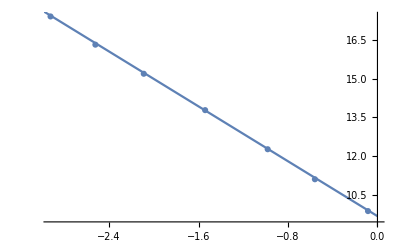

8.9-8.35454×10^-9 P

-1.19695×10^8

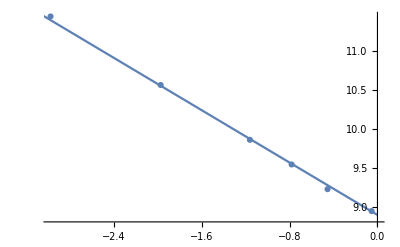

8.65+6.50092×10^-9 P

1.53824×10^8

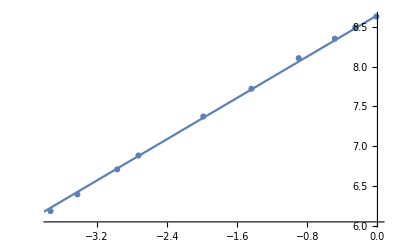

```mathematica
(*Plotting the Stress vs Transition Temperature Data &Computing Slopes*)
dP110bdT=Table[((P110[[i,1]]-P110[[i+1,1]])/(P110[[i,2]]-P110[[i+1,2]])),{i,1,Length[P110]-1}];
T110[P_]:=9.7+(Total[dP110bdT]/Length[dP110bdT])^-1*P
T110[P]
Total[dP110bdT]/Length[dP110bdT]
p1=ListPlot[P110, PlotMarkers->Automatic];
p2 = Plot[T110[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
dP100bdT=Table[((P100[[i,1]]-P100[[i+1,1]])/(P100[[i,2]]-P100[[i+1,2]])),{i,1,Length[P100]-1}];
T100[P_]:=8.9+(Total[dP100bdT]/Length[dP100bdT])^-1*P
T100[P]
Total[dP100bdT]/Length[dP100bdT]
p1=ListPlot[P100, PlotMarkers->Automatic];
p2 = Plot[T100[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
dP001bdT=Table[((P001[[i,1]]-P001[[i+1,1]])/(P001[[i,2]]-P001[[i+1,2]])),{i,1,Length[P001]-1}];
T001[P_]:=8.65+(Total[dP001bdT]/Length[dP001bdT])^-1*P
T001[P]
Total[dP001bdT]/Length[dP001bdT]
p1=ListPlot[P001, PlotMarkers->Automatic];
p2 = Plot[T001[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
```

```mathematica
(*Computing Claussius Clayperon*)
K1=Total[dP100bdT]/Length[dP100bdT]
K2=Total[dP110bdT]/Length[dP110bdT]
K3=Total[dP001bdT]/Length[dP001bdT]
Print["--------------------------------------------------"]
Print["The Δη of Cl-Cp for σ_100 is= ",-K1*(Subscript[a, 0]/(â)-a/(â))]
Print["The Δη of Cl-Cp for σ_110 is= ",-K2*(Tr[{{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}.UT1]-Tr[{{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}.Qq[0,0,1,Pi/4-ArcTan[b,a]].UO2])]
Print["The Δη of Cl-Cp for σ_001 is= ",-K3*(Subscript[c, 0]/(â)-c/(â))]
(Subscript[c, 0]/(â)-c/(â))
Tr[{{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}.UT1]
Qq[0,0,1,Pi/4-ArcTan[b,a]].UO2//MatrixForm
Tr[{{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}.Qq[0,0,1,Pi/4-ArcTan[b,a]].UO2]
```

-1.19695×10^8

-3.78501×10^7

1.53824×10^8

--------------------------------------------------

The Δη of Cl-Cp for σ_100 is= 350402.

The Δη of Cl-Cp for σ_110 is= 8223.35

The Δη of Cl-Cp for σ_001 is= -48185.2

0.000313248

0.741126

(0.738194 | -0.00273523 | 0.
0.00271518 | 0.743644 | 0.
0. | 0. | 1.82029)

0.740909

--------------------------------------------------

13.1695

{{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}

0.78172

(0.99605 | 0 | 0
0 | 1.0034 | 0
0 | 0 | 1.00307)

(0.996043 | -0.00369064 | 0.
0.00366359 | 1.0034 | 0.
0. | 0. | 1.00307)

((as+bs) Cos[μ]+(as-bs) Sin[μ])/(2 as_0)

Δη_110 is 11095.7

(0.00395674 | 0.00369064 | 0.
-0.00366359 | -0.00339749 | 0.
0. | 0. | -0.00307361)

0.000293149

The Δη of Cl-Cp for σ_100 is= 472797.

The Δη of Cl-Cp for σ_001 is= -26466.6!!! This turns out to be the wrong sign since c/c_0 from exp have the wrong sign!!!

The c of the Orthorhombic phase from Cl-Cp for σ_001 is= 13.1695

The Δη of Cl-Cp for σ_110 is= 11095.7